```mathematica
detailIDdr={{AL, AK, AZ, AR, CA, CO, CT, DC, DE,FL,GA,HI,ID,IL,IN,IA,KS,KY,LA,ME,MD,MA,MI,MN,MS,MO,MT,NE,NV,NH,NJ,NM,NY,NC,ND,OH,OK,OR,PA,RI,SC,SD,TN,TX,UT,VT,VA,WA,WV,WI,WY},{416468,416471,416484,416491,416498,416505,416508,416623,416511,417861,416514,416520,416523,416532,416542,416545,416554,416557,416560,416569,416584,416593,416599,416602,416612,416619,416487,416490,416496,416502,416516,416526,416529,416534,416539,416548,416551,416590,416595,416605,416608,416611,416617,416632,416636,416639,416642,416645,416648,416653,416654},
{416469,416472,416485,416493,416500,416506,416509,416624,416512,417866,416515,416521,416524,416537,416543,416546,416555,416558,416561,416570,416585,416594,416600,416603,416614,416621,416488,416492,416497,416503,416518,416527,416530,416535,416540,416549,416552,416591,416597,416606,416609,416613,416618,416634,416637,416640,416643,416646,416649,416651,416655}};
```

```mathematica
Dimensions[detailIDdr]
```

{3,51}

```mathematica
ev=Import["http://www.electoral-vote.com/evp2008/Pres/Excel/today.csv"];
```

```mathematica
ev[[1]]
```

{State,EV,D,R,I,Date,D>9,D5-9,D<5,Tie,R<5,R5-9,R>9,Pollster-len}

```mathematica
ev[[2;;-2,1]]
```

{Alabama,Alaska,Arizona,Arkansas,California,Colorado,Connecticut,D.C.,Delaware,Florida,Georgia,Hawaii,Idaho,Illinois,Indiana,Iowa,Kansas,Kentucky,Louisiana,Maine,Maryland,Massachusetts,Michigan,Minnesota,Mississippi,Missouri,Montana,Nebraska,Nevada,New Hampshire,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oklahoma,Oregon,Pennsylvania,Rhode Island,South Carolina,South Dakota,Tennessee,Texas,Utah,Vermont,Virginia,Washington,West Virginia,Wisconsin,Wyoming}

```mathematica
ev[[2;;-2,2]]
```

{9,3,10,6,55,9,7,3,3,27,15,4,4,21,11,7,6,8,9,4,10,12,17,10,6,11,3,5,5,4,15,5,31,15,3,20,7,7,21,4,8,3,11,34,5,3,13,11,5,10,3}

```mathematica
datad=Table[Drop[Import["http://data.intrade.com/graphing/jsp/downloadClosingPrice.jsp?contractId="<>ToString[detailIDdr[[2,i]] ]],1],{i,51}];
```

```mathematica
datar=Table[Drop[Import["http://data.intrade.com/graphing/jsp/downloadClosingPrice.jsp?contractId="<>ToString[detailIDdr[[3,i]] ]],1],{i,51}];
```

```mathematica
datad[[1,-1,1]]
```

Oct 2, 2008

```mathematica
datad[[5,662;;666]]
```

{{Sep 9, 2008,91.2,91.2,91.2,91.2,40},{Sep 10, 2008,91.2,91.2,91.2,91.2,0},{Sep 11, 2008,91,91,91,91,0},{Sep 12, 2008,92,91,92,91,34},{Sep 13, 2008,90.5,90.5,90.5,90,10}}

```mathematica
(*datad[[5,664,2;;-1]]=datad[[5,663,2;;-1]] 
data error: CA price on 9.11=3 instead of 91.2*)
```

```mathematica
(*another error Sep 15 R price in MI is 98*)
datar[[23,655;;660]]
```

{{Sep 13, 2008,36.1,36.1,36.1,38.9,1},{Sep 14, 2008,38.5,36.2,40,39.9,35},{Sep 15, 2008,98,98,98,98,0},{Sep 16, 2008,36.2,36.2,39.9,36.2,9},{Sep 17, 2008,38,35,38,35,31},{Sep 18, 2008,35.1,35.1,35.1,35,11}}

```mathematica
datar[[23,657,2;;-1]]=datar[[23,656,2;;-1]]
```

{38.5,36.2,40,39.9,35}

```mathematica
closed=datad[[All,All,5]];
closer=datar[[All,All,5]];
```

```mathematica
window=90;window1=window+1;
```

```mathematica
returnsd=Table[Log[closed[[i,j-1]]/closed[[i,j]]],{i,51},{j,-window,-1}];
```

```mathematica
returnsr=Table[Log[closer[[i,j-1]]/closer[[i,j]]],{i,51},{j,-window,-1}];
```

```mathematica
chanced=Table[closed[[i,-window1;;-1]]/(closed[[i,-window1;;-1]]+closer[[i,-window1;;-1]]),{i,51}];
```

```mathematica
returnsc=Table[Log[chanced[[i,j-1]]/chanced[[i,j]]],{i,51},{j,-window,-1}];
```

```mathematica
chanced[[All,-1]]//N
```

{0.03,0.077,0.05,0.0997009,0.934,0.693756,0.925,0.97,0.94,0.522,0.149758,0.977,0.03,0.96,0.382353,0.834826,0.0682927,0.087,0.092,0.902248,0.943,0.965,0.771484,0.818731,0.075,0.43,0.191929,0.0865385,0.567308,0.635,0.907,0.793814,0.956,0.480269,0.108911,0.57,0.043,0.909574,0.80695,0.95,0.08867,0.08,0.076,0.073,0.02,0.95,0.585149,0.89613,0.178744,0.816943,0.042}

```mathematica
datad[[1,-window,1]]
```

Jul 6, 2008

```mathematica
winning=Table[Total[Table[If[chanced[[i,-j]]>.5,ev[[2;;-2,2]][[i]],0],{i,51}]],{j,window}]
```

{338,338,338,311,338,311,311,311,291,278,278,273,278,293,293,273,273,273,273,273,273,273,273,273,273,311,311,311,311,311,293,293,293,293,306,293,293,306,306,306,311,306,291,291,306,306,306,306,306,311,311,311,298,306,306,311,306,306,311,311,311,311,311,306,311,311,311,311,311,311,311,311,311,311,311,311,322,311,311,311,311,311,311,322,322,322,322,322,322,322}

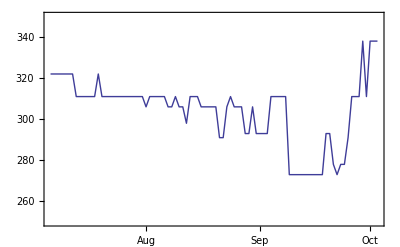

```mathematica
DateListPlot[Reverse[winning],{2008,7,6},Joined->True,PlotRange->{Automatic,{250,350}}]
```

```mathematica
timeleft=DateDifference[DateList[][[1;;3]],{2008,11,4}]
```

33

```mathematica
liquidityd=Table[Count[returnsd[[i,-window;;-1]],n_/;n!=0],{i,51}]
```

{8,29,19,13,38,48,31,1,18,53,40,53,18,17,44,43,35,25,43,29,28,14,40,46,29,49,37,15,54,47,39,40,31,38,30,51,13,40,49,13,27,32,11,37,3,31,50,21,32,45,13}

```mathematica
liquidityr=Table[Count[returnsr[[i,-window;;-1]],n_/;n!=0],{i,51}]
```

{12,31,15,22,42,54,36,60,14,54,34,14,9,11,41,36,32,13,27,36,29,23,45,53,28,49,34,13,56,47,47,42,30,37,27,52,16,52,51,14,21,24,15,27,5,32,51,23,27,47,4}

```mathematica
{Mean[liquidityd],Mean[liquidityr]}//N
```

{31.5686,31.6471}

```mathematica
Needs["Histograms`"]
```

```mathematica
<<MultivariateStatistics`
```

```mathematica
cvard=Table[,{51},{51}];
For[j=1,j≤51,j++,
For[i=1, i≤51, i++, cvard[[j,i]]=Covariance[returnsd[[i]],returnsd[[j]] ]]]
```

```mathematica
cvarr=Table[,{51},{51}];
For[j=1,j≤51,j++,
For[i=1, i≤51, i++, cvarr[[j,i]]=Covariance[returnsr[[i]],returnsr[[j]] ]]]
```

```mathematica
closed=Table[closed[[i,-window;;-1]],{i,51}];
```

```mathematica
closer=Table[closer[[i,-window;;-1]],{i,51}];
```

```mathematica
simsdet=Table[
ds=Exp[Transpose[RandomReal[MultinormalDistribution[Table[0,{51}],cvard],timeleft]]];
rs=Exp[Transpose[RandomReal[MultinormalDistribution[Table[0,{51}],cvarr],timeleft]]];
endd=closed[[All,-1]];
endr=closer[[All,-1]];
For[j=1,j≤51,j++,Do[endd[[j]]=endd[[j]] ds[[j,i]];endr[[j]]=endr[[j]] rs[[j,i]],{i,timeleft}]];
chanced=endd/(endd+endr);
Table[If[chanced[[i]]>.5,ev[[2;;-2,2]][[i]],0],{i,51}],{5000}
];
```

```mathematica
sims=Map[Total,simsdet];
```

```mathematica
Count[sims,n_/;n>268]/Length[sims]//N
```

0.9916

```mathematica
{Mean[sims],StandardDeviation[sims]}//N
```

{330.17,24.986}

```mathematica
counts=Table[Count[sims,n_/;n==i],{i,538}];
```

```mathematica
counts[[269]]/5000.
```

0.002

```mathematica
mode=Position[counts,Max[counts]][[1,1]]
```

353

```mathematica
chanced=Table[closed[[i,-window;;-1]]/(closed[[i,-window;;-1]]+closer[[i,-window;;-1]]),{i,51}];today=Total[Table[If[chanced[[i,-1]]>.5,ev[[2;;-2,2]][[i]],0],{i,51}]]
```

338

```mathematica
counts[[today]] ==mode(*Everything breaking exactly like today is the mode of the distribution*)
```

False

```mathematica
hr=Histogram[Select[sims, #<269&],Ticks->{Table[10x,{x,21,41}],None},HistogramCategories->Table[x,{x,538}],BarStyle->Red];
```

```mathematica
hd=Histogram[Select[sims, #>268&],Ticks->{Table[10x,{x,21,41}],None},HistogramCategories->Table[x,{x,538}],BarStyle->Blue];
```

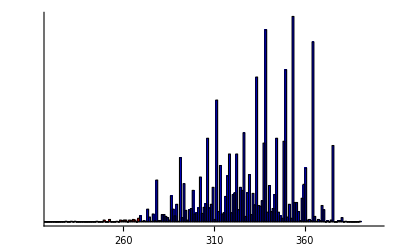

```mathematica
Show[hr,hd,PlotRange->{{220,400},{0,Max[counts]}}]
```

```mathematica
{Table[i,{i,250,310}],Table[Count[sims,n_/;n==i],{i,250,310}]}//MatrixForm//N
```

(250. | 251. | 252. | 253. | 254. | 255. | 256. | 257. | 258. | 259. | 260. | 261. | 262. | 263. | 264. | 265. | 266. | 267. | 268. | 269. | 270. | 271. | 272. | 273. | 274. | 275. | 276. | 277. | 278. | 279. | 280. | 281. | 282. | 283. | 284. | 285. | 286. | 287. | 288. | 289. | 290. | 291. | 292. | 293. | 294. | 295. | 296. | 297. | 298. | 299. | 300. | 301. | 302. | 303. | 304. | 305. | 306. | 307. | 308. | 309. | 310.
0. | 0. | 4. | 0. | 0. | 0. | 1. | 0. | 3. | 2. | 3. | 3. | 0. | 3. | 2. | 4. | 3. | 0. | 6. | 10. | 1. | 2. | 1. | 21. | 8. | 1. | 13. | 2. | 69. | 2. | 2. | 12. | 12. | 9. | 7. | 3. | 43. | 21. | 10. | 29. | 1. | 106. | 7. | 63. | 19. | 3. | 20. | 22. | 52. | 13. | 15. | 23. | 74. | 14. | 24. | 30. | 138. | 23. | 29. | 57. | 4.)

```mathematica
Table[Count[sims,n_/;n>i]/Length[sims],{i,229,339,10}]//N
```

{0.9996,0.9992,0.9984,0.9964,0.9896,0.9656,0.936,0.8748,0.7894,0.6718,0.5486,0.3732}

```mathematica
Table[Count[sims,n_/;n-10<i<n]/Length[sims],{i,229,339,10}]//N
```

{0.0004,0.0002,0.0016,0.0048,0.0236,0.0238,0.0586,0.074,0.1146,0.1076,0.1722,0.0894}

```mathematica
chanced=Table[closed[[i,-window;;-1]]/(closed[[i,-window;;-1]]+closer[[i,-window;;-1]]),{i,51}];
```

```mathematica
{Extract[chanced[[All,-1]],Position[chanced[[All,-1]],n_/;.3<n<.8]]//N,Extract[detailIDdr[[1]],Position[chanced[[All,-1]],n_/;.3<n<.8]],swingev=Extract[ev[[2;;-2,2]],Position[chanced[[All,-1]],n_/;.3<n<.80]]}//MatrixForm
```

(0.693756 | 0.522 | 0.382353 | 0.771484 | 0.43 | 0.567308 | 0.635 | 0.793814 | 0.480269 | 0.57 | 0.585149
CO | FL | IN | MI | MO | NV | NH | NM | NC | OH | VA
9 | 27 | 11 | 17 | 11 | 5 | 4 | 5 | 15 | 20 | 13)

```mathematica
Total[swingev]
swingevD=Total[Extract[ev[[2;;-2,2]],Position[chanced[[All,-1]],n_/;.5<n<.7]]]
swingevD/Total[swingev]//N
```

137

78

0.569343

```mathematica
detailIDdr[[1,{36,39}]]
chanced[[{36,39},-1]]//N
ev[[2;;-2,2]][[{36,39}]]
```

{OH,PA}

{0.57,0.80695}

{20,21}

```mathematica
Correlation[returnsc[[36]],returnsc[[39]]]
```

0.357206

```mathematica
ohpa=Table[Switch[Total[simsdet[[i,{36,39}]]],0,"Neither",20,"OH",21,"PA",41,"Both"],{i,5000}];
```

```mathematica
Count[ohpa,"PA"]/50.
100 chanced[[39,-1]]( 1-chanced[[36,-1]])
```

24.44

34.6988

```mathematica
Count[ohpa,"OH"]/50.
100 chanced[[36,-1]]( 1-chanced[[39,-1]])
```

0.02

11.0039

```mathematica
Count[ohpa,"Both"]/50.
100 chanced[[39,-1]] chanced[[36,-1]]
```

75.5

45.9961

```mathematica
Count[ohpa,"Neither"]/50.
100 ( 1-chanced[[39,-1]]) ( 1-chanced[[36,-1]])
```

0.04

8.30116

```mathematica
(*Very little chance of winning Ohio but not Pennsylvania.  Probabilities very different from if OH & PA were independent*)
```

```mathematica
chanced=Table[closed[[i,-window;;-1]]/(closed[[i,-window;;-1]]+closer[[i,-window;;-1]]),{i,51}];
```

```mathematica
sbys={Table[Count[simsdet[[All,i]],n_/;n>0]/Length[simsdet],{i,51}]//N, detailIDdr[[1]],chanced[[All,-1]]//N}//MatrixForm
```

(0. | 0.014 | 0. | 0. | 0.9994 | 0.9912 | 0.9976 | 1. | 0.9962 | 0.6006 | 0.0036 | 1. | 0. | 1. | 0.2344 | 1. | 0.0002 | 0. | 0.0004 | 0.9914 | 1. | 1. | 0.9904 | 0.9522 | 0. | 0.2642 | 0.0024 | 0.0618 | 0.7488 | 0.934 | 0.9848 | 1. | 1. | 0.4648 | 0. | 0.7552 | 0. | 0.9966 | 0.9994 | 1. | 0. | 0.001 | 0.004 | 0. | 0. | 1. | 0.8188 | 0.9996 | 0.0128 | 0.9826 | 0.
AL | AK | AZ | AR | CA | CO | CT | DC | DE | FL | GA | HI | ID | IL | IN | IA | KS | KY | LA | ME | MD | MA | MI | MN | MS | MO | MT | NE | NV | NH | NJ | NM | NY | NC | ND | OH | OK | OR | PA | RI | SC | SD | TN | TX | UT | VT | VA | WA | WV | WI | WY
0.03 | 0.077 | 0.05 | 0.0997009 | 0.934 | 0.693756 | 0.925 | 0.97 | 0.94 | 0.522 | 0.149758 | 0.977 | 0.03 | 0.96 | 0.382353 | 0.834826 | 0.0682927 | 0.087 | 0.092 | 0.902248 | 0.943 | 0.965 | 0.771484 | 0.818731 | 0.075 | 0.43 | 0.191929 | 0.0865385 | 0.567308 | 0.635 | 0.907 | 0.793814 | 0.956 | 0.480269 | 0.108911 | 0.57 | 0.043 | 0.909574 | 0.80695 | 0.95 | 0.08867 | 0.08 | 0.076 | 0.073 | 0.02 | 0.95 | 0.585149 | 0.89613 | 0.178744 | 0.816943 | 0.042)

```mathematica
Table[Extract[sbys[[1,i]],Position[sbys[[1,1]],n_/;.02<n<.98]],{i,3}]//MatrixForm
```

(0.6006 | 0.2344 | 0.9522 | 0.2642 | 0.0618 | 0.7488 | 0.934 | 0.4648 | 0.7552 | 0.8188
FL | IN | MN | MO | NE | NV | NH | NC | OH | VA
0.522 | 0.382353 | 0.818731 | 0.43 | 0.0865385 | 0.567308 | 0.635 | 0.480269 | 0.57 | 0.585149)

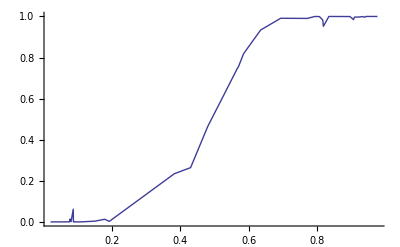

```mathematica
ListPlot[Sort[Transpose[{sbys[[1,3]],sbys[[1,1]]}]],Joined->True,PlotStyle->Thick]
```